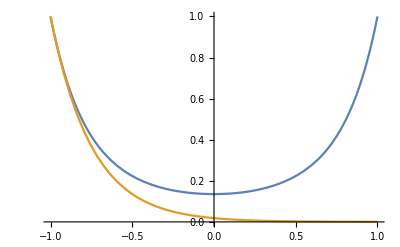

```mathematica
Plot[{Exp[2(t^2-1)],Exp[-4(t+1)]},{t,-1,1}]
```

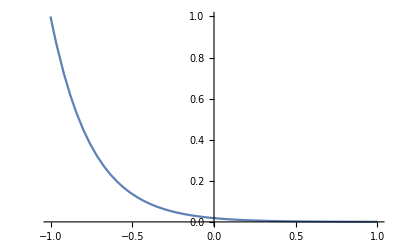

```mathematica
Plot[Exp[-4(t+1)],{t,-1,1},PlotRange->{0,1}]
```

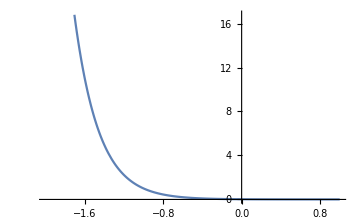

```mathematica
Show[Plot[Exp[-4(t+1)],{t,-2,1}],ImageSize->Medium]
```

```mathematica
Rasterize[%5,"Image"]
```

```mathematica
-Graphics-
Clear[y]
```

-Graphics-

```mathematica
DSolve[{ϵ y'[t]==t y[t]+ϵ,y[-1]==1},y[t],{t,-1,1}]
```

{{y[t]→1/2 ⅇ^((-1+t^2)/(2 ϵ)) (2+ⅇ^(1/2/ϵ) √(2 π) √ϵ Erf[1/(√2 √ϵ)]+ⅇ^(1/2/ϵ) √(2 π) √ϵ Erf[t/(√2 √ϵ)])}}

```mathematica
ϵ:=.25
```

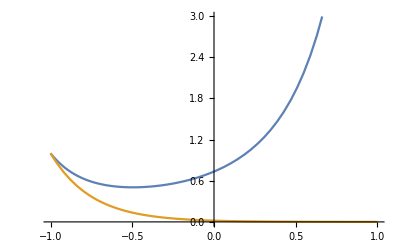

```mathematica
Plot[{1/2 ⅇ^((-1+t^2)/(2 ϵ)) (2+ⅇ^(1/2/ϵ) √(2 π) √ϵ Erf[1/(√2 √ϵ)]+ⅇ^(1/2/ϵ) √(2 π) √ϵ Erf[t/(√2 √ϵ)]),Exp[-4(t+1)]},{t,-1,1}]
```

```mathematica
-Graphics-
DSolve[{y'[t]+t y[t]==t,y[0]==2},y[t],{t,0,1}]
```

-Graphics-

{{y[t]→1+ⅇ^(-t^2/2)}}

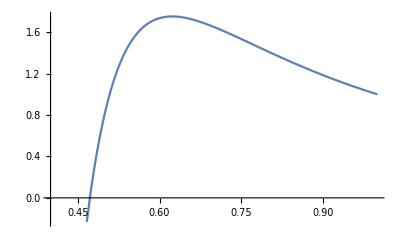

```mathematica
Plot[1/x^2+(.1)/2(x-1/x^6),{x,0.4,1}]
```

```mathematica
NDSolve[{(x^2+.05 y[x])y'[x]+2x y[x]==(3*.05)/(2y[x]),y[1]==1},y[x],{x,-1,1}]
```

{{y[x]→InterpolatingFunction[{{-1., 1.}}, <>][x]}}

```mathematica
%62⟦1,1,2⟧
```

InterpolatingFunction[{{-1., 1.}}, <>][x]

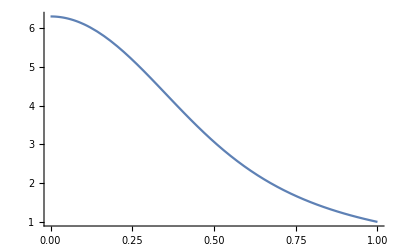

```mathematica
Plot[%63,{x,.,1.}]
```

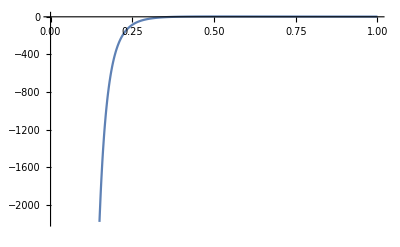

```mathematica
Plot[1/x^2-Sqrt[.05]x^2+Sqrt[.05]Sqrt[36+x^4]+(.05)/2(x-1/x^6),{x,0,1}]
```

```mathematica
Sqrt[.1]
```

0.316228